```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
typelist=Table[Import["type_"<>ToString[i]<>".txt","CSV"],{i,20}]
```

{{{0,0},{161,402},{161,423},{161,426},{162,398},{162,405},{162,422},{163,308},{163,391},{163,412},{163,413},{164,308},{164,313},{164,394},{164,400},{164,404},{164,420},{165,302},{165,306},{165,307},{165,308},{165,310},{165,311},{165,312},{165,313},{165,314},{165,315},{165,316},{165,318},{165,319},{165,391},{165,412},{166,301},{166,302},{166,303},{166,304},{166,305},{166,306},{166,307},{166,308},{166,309},{166,310},{166,311},{166,312},{166,313},{166,314},{166,315},{166,316},{166,317},{166,320},{166,321},{166,393},{166,397},{166,405},{166,415},{167,300},{167,301},{167,302},{167,303},{167,304},{167,305},{167,306},18659,{539,304},{539,305},{539,306},{539,307},{539,308},{539,309},{539,310},{539,311},{539,312},{539,313},{539,321},{539,322},{539,325},{539,327},{539,331},{539,333},{539,357},{539,362},{539,365},{539,366},{540,296},{540,297},{540,298},{540,302},{540,303},{540,304},{540,305},{540,307},{540,308},{540,309},{540,310},{540,311},{540,312},{540,313},{540,322},{540,324},{540,352},{540,356},{540,365},{541,305},{541,306},{541,307},{541,308},{541,310},{541,321},{541,322},{541,356},{541,357},{541,358},{541,365},{542,321},{542,322},{542,326},{542,357},{542,365},{543,319},{543,322},{543,325},{543,357},{546,365},{547,357},{548,357}},18,{{0,0}}}
 |  |  |  |

```mathematica
typelist[[1]]
```

{{0,0},{161,402},{161,423},{161,426},{162,398},{162,405},{162,422},{163,308},{163,391},{163,412},{163,413},{164,308},{164,313},{164,394},{164,400},{164,404},{164,420},{165,302},{165,306},{165,307},{165,308},{165,310},{165,311},{165,312},{165,313},{165,314},{165,315},{165,316},{165,318},{165,319},{165,391},{165,412},{166,301},{166,302},{166,303},{166,304},{166,305},{166,306},{166,307},{166,308},{166,309},{166,310},{166,311},{166,312},{166,313},{166,314},{166,315},{166,316},{166,317},{166,320},{166,321},{166,393},{166,397},{166,405},{166,415},{167,300},{167,301},{167,302},{167,303},{167,304},{167,305},{167,306},{167,307},18657,{539,303},{539,304},{539,305},{539,306},{539,307},{539,308},{539,309},{539,310},{539,311},{539,312},{539,313},{539,321},{539,322},{539,325},{539,327},{539,331},{539,333},{539,357},{539,362},{539,365},{539,366},{540,296},{540,297},{540,298},{540,302},{540,303},{540,304},{540,305},{540,307},{540,308},{540,309},{540,310},{540,311},{540,312},{540,313},{540,322},{540,324},{540,352},{540,356},{540,365},{541,305},{541,306},{541,307},{541,308},{541,310},{541,321},{541,322},{541,356},{541,357},{541,358},{541,365},{542,321},{542,322},{542,326},{542,357},{542,365},{543,319},{543,322},{543,325},{543,357},{546,365},{547,357},{548,357}}
 |  |  |  |

```mathematica
typelist[[2]]
```

{{0,0},{158,345},{159,402},{159,406},{159,414},{159,416},{160,344},{160,398},{160,399},{160,400},{160,401},{160,402},{160,403},{160,404},{160,405},{160,406},{160,407},{160,408},{160,409},{160,410},{160,413},{160,414},{160,415},{160,416},{160,417},{160,420},{160,421},{160,422},{160,423},{160,426},{161,395},{161,397},{161,398},{161,399},{161,400},{161,401},{161,403},{161,404},{161,405},{161,406},{161,407},{161,408},{161,409},{161,410},{161,411},{161,412},{161,413},{161,414},{161,415},{161,416},{161,417},{161,418},{161,419},{161,420},{161,421},{161,422},{161,424},{161,425},{161,427},{161,429},{161,430},{161,431},{162,349},37275,{545,362},{545,363},{545,364},{545,365},{545,366},{545,367},{545,378},{545,390},{546,321},{546,322},{546,323},{546,324},{546,325},{546,326},{546,327},{546,328},{546,329},{546,330},{546,331},{546,336},{546,337},{546,338},{546,339},{546,340},{546,341},{546,356},{546,357},{546,358},{546,359},{546,360},{546,361},{546,362},{546,363},{546,364},{546,366},{547,323},{547,324},{547,325},{547,326},{547,327},{547,328},{547,329},{547,330},{547,338},{547,340},{547,350},{547,358},{547,359},{547,360},{547,361},{547,362},{547,363},{547,365},{548,324},{548,325},{548,326},{548,327},{548,358},{548,359},{548,360},{548,362},{549,348},{549,349}}
 |  |  |  |

```mathematica
typelist[[3]]
```

{{0,0},{156,349},{156,350},{156,351},{156,352},{157,346},{157,347},{157,348},{157,349},{157,351},{158,344},{158,347},{158,348},{158,349},{158,350},{158,351},{158,352},{158,362},{158,363},{158,364},{159,343},{159,344},{159,345},{159,346},{159,347},{159,348},{159,349},{159,350},{159,352},{159,353},{159,362},{159,363},{159,364},{159,365},{159,366},{159,367},{160,338},{160,339},{160,342},{160,343},{160,345},{160,346},{160,347},{160,348},{160,349},{160,350},{160,351},{160,352},{160,353},{160,362},{160,363},{160,364},{160,365},{160,366},{160,367},{160,368},{160,375},{160,376},{160,377},{161,332},{161,335},{161,336},{161,337},35318,{547,377},{547,378},{547,379},{547,380},{547,381},{548,342},{548,343},{548,344},{548,345},{548,347},{548,348},{548,349},{548,350},{548,352},{548,353},{548,354},{548,355},{548,356},{548,369},{548,370},{548,371},{548,372},{548,373},{548,374},{548,375},{548,376},{548,377},{548,378},{548,379},{548,380},{548,381},{549,344},{549,345},{549,346},{549,347},{549,350},{549,351},{549,352},{549,353},{549,354},{549,355},{549,356},{549,357},{549,370},{549,371},{549,372},{549,373},{549,374},{549,375},{549,376},{549,377},{549,378},{549,379},{549,380},{550,345},{550,347},{550,348},{550,349},{550,350},{550,351},{550,355},{550,372},{550,373}}
 |  |  |  |

```mathematica
typelist[[9]]
```

{{0,0},{210,509},{216,334},{218,335},{219,291},{222,511},{223,365},{224,291},{224,509},{225,344},{225,478},{232,296},{234,337},{235,457},{238,482},{242,329},{242,491},{243,269},{244,449},{244,554},{245,394},{247,301},{249,542},{250,313},{253,303},{253,309},{253,466},{253,486},{254,469},{256,304},{256,448},{257,467},{258,315},{259,318},{259,453},{261,263},{262,447},{262,464},{263,361},{265,330},{266,454},{267,325},{267,436},{268,447},{268,474},{269,331},{270,337},{271,340},{274,345},{274,439},{274,442},{276,310},{277,399},{277,476},{278,443},{279,459},{280,450},{280,452},{281,329},{281,431},{285,290},{285,417},{285,437},{288,448},{289,351},{290,355},{290,421},{290,433},{291,328},{292,317},{292,412},{293,277},{294,390},{295,411},{295,465},{296,300},{297,397},{297,408},{297,507},{298,410},{299,363},{300,291},{304,316},{305,262},{306,464},{307,516},{309,472},{310,409},{311,316},{312,419},{313,345},{313,459},{314,476},{315,249},{315,452},{315,503},{316,444},{318,223},{318,436},{319,438},{327,443},{332,326},{332,371},{334,134},{335,287},{335,376},{338,466},{340,269},{340,336},{342,376},{343,181},{343,351},{346,264},{346,289},{346,470},{349,358},{352,380},{353,287},{356,180},{358,309},{361,356},{362,351},{364,346},{371,396},{375,413},{375,449},{380,241},{380,440},{381,343},{383,235},{390,279},{392,304},{392,396},{392,441},{394,440},{397,217},{398,246},{399,300},{401,469},{403,301},{408,341},{409,337},{411,259},{413,194},{416,348},{419,233},{421,404},{423,403},{425,271},{427,344},{430,451},{430,486},{437,256},{457,441},{463,398},{467,362},{498,357}}

```mathematica
typelist[[12]]
```

{{0,0}}

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

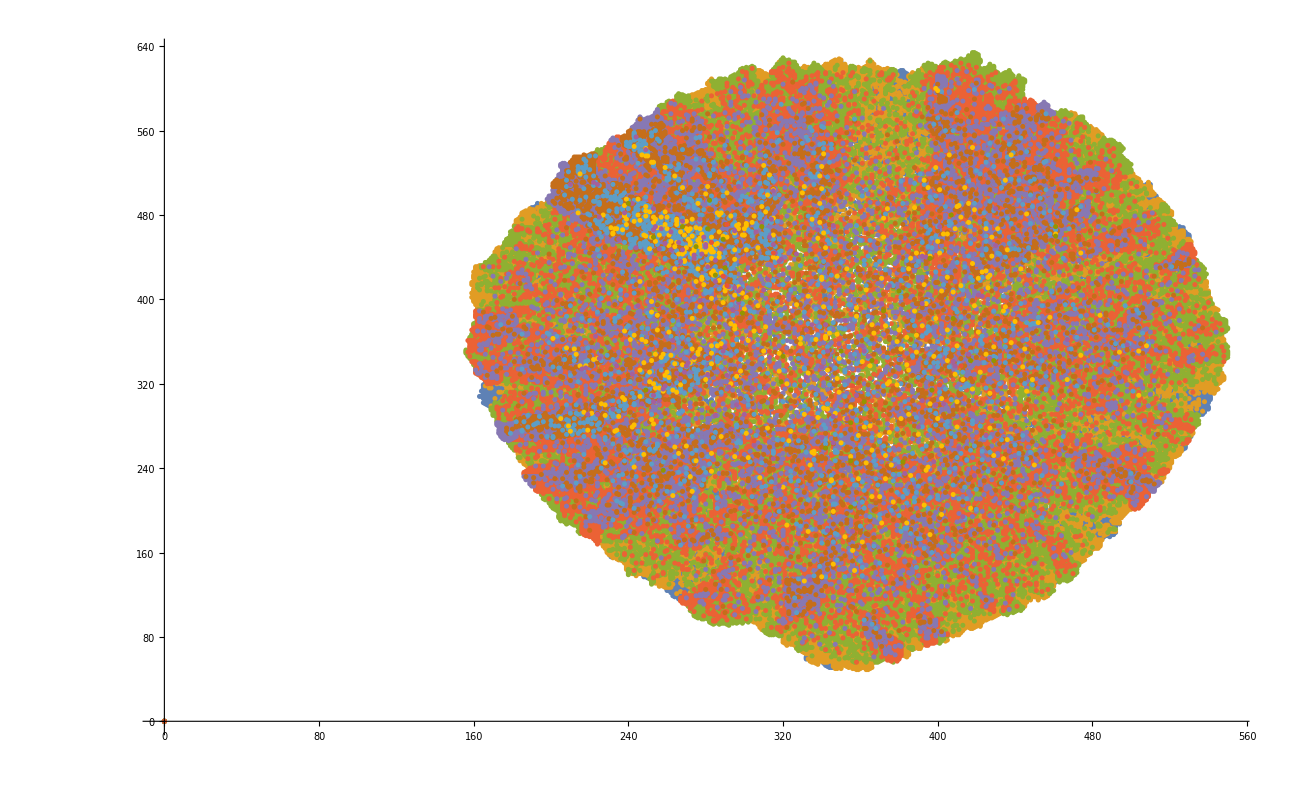

Part::partw: Part 3 of {0, 0} does not exist.

```mathematica
ListPlot[{typelist[[1]],typelist[[2]],typelist[[3]],typelist[[4]],typelist[[5]],typelist[[6]],typelist[[7]],typelist[[8]],typelist[[9]],typelist[[10]],typelist[[11]], typelist[[12]], typelist[[13]], typelist[[14]], typelist[[15]], typelist[[16]], typelist[[17]], typelist[[18]], typelist[[19]]}]
```

```mathematica
data =Import["xi.txt", "CSV"]
```

{{0,8},{1,2},{2,0},{3,1},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

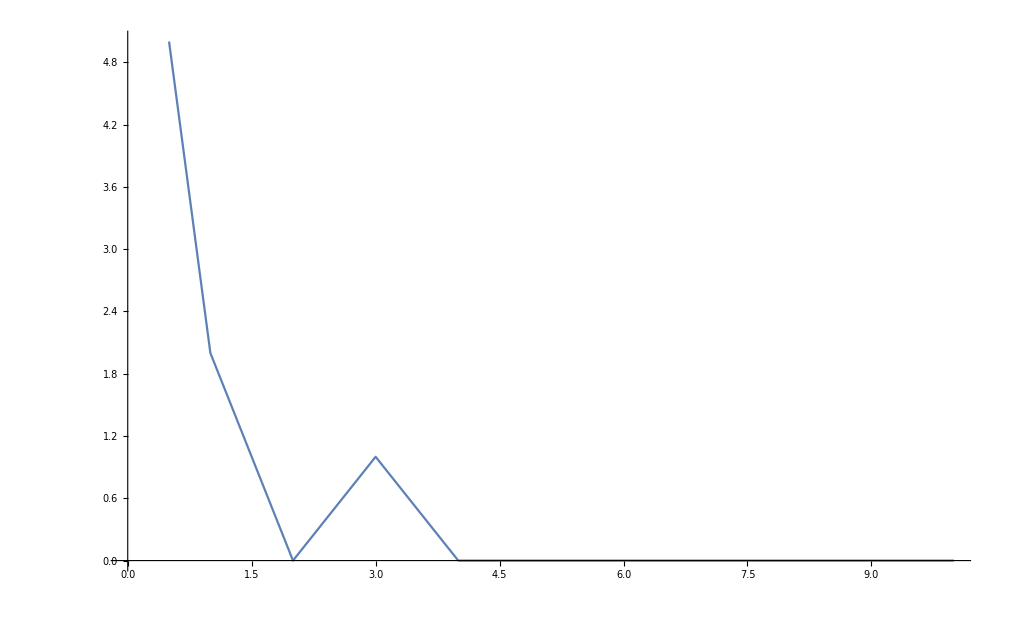

```mathematica
ListLinePlot[data]
```